```mathematica
dx=-x+a/(1+Exp[-4(x-b)])
```

a/(1+ⅇ^(-4 (-b+x)))-x

```mathematica
Solve[dx==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[a/(1+ⅇ^(-4 (-b+x)))-x==0,x]

```mathematica
D[Normal[Series[dx,{x,b,3}]]]
```

a/2-b+(-1+a) (-b+x)-4/3 a (-b+x)^3

```mathematica
ddx=D[dx,x]
```

-1+(4 a ⅇ^(-4 (-b+x)))/((1+ⅇ^(-4 (-b+x)))^2)

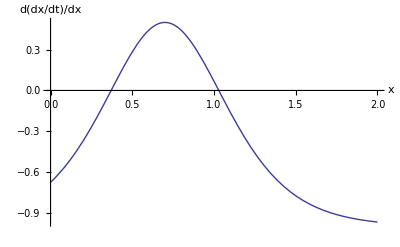

```mathematica
Plot[ddx/.{a->1.5,b->0.7},{x,0,2.0},AxesLabel->{"x","d(dx/dt)/dx"}]
```

```mathematica
xplus=Log[2 a-1+Sqrt[(-1-2 a)^2-1]]/-4+b
xminu=Log[2 a-1-Sqrt[(-1-2 a)^2-1]]/-4+b
```

b-1/4 Log[-1+√(-1+(-1-2 a)^2)+2 a]

b-1/4 Log[-1-√(-1+(-1-2 a)^2)+2 a]

We can solve for a curve in α × β space on which f.p. are possible.

{{b→1/(4 (a+√(a (1+a))))(2 a+a Log[-1+√(-1+(-1-2 a)^2)+2 a]+√(a (1+a)) Log[-1+√(-1+(-1-2 a)^2)+2 a])}}

{{b→1/(4 (-a+√(a (1+a))))(-2 a-a Log[-1-√(-1+(-1-2 a)^2)+2 a]+√(a (1+a)) Log[-1-√(-1+(-1-2 a)^2)+2 a])}}

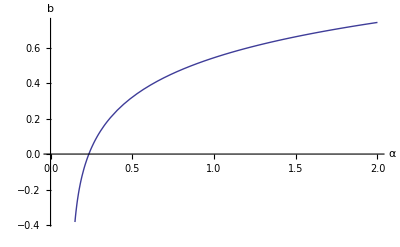

```mathematica
bsolnp=Solve[(dx/.x->xplus)==0,b]
bsolnm=Solve[(dx/.x->xminu)==0,b]
Plot[b/.{bsolnm,bsolnp},{a,0,2},AxesLabel->{"α","b"}]
```

But I don’t really think that’s useful.